Last modified on: Tuesday, July 10, 2018 at 22:56

Author Info

Nguyen Ton

Tuseeta Banejee

University of Virginia

Poster Session Content

Predict the orientation of an image

Goal: estimate  the orientation of an image using neural network. When horizon or other horizontal and vertical lines in the image are missing, determining the rotation of an image can be very hard. Fortunately, convolution network can learn the feature and predict the orientation if we give the network enough training data.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics-

Several approaches are used:
1. Use LeNet model on MNIST dataset: 97.7% accuracy with rotation angle in step of 30 degree from 0 to 330 degree. 60k images (28x28x1) on training set, 10k in testing, 10k in validation set.
2. Use ImageNet dataset with Ademxapp model for training: 90% accuracy on 10k images (224x224x3) for training, 1k for testing, 1k for validation. Rotate from 0 to 360 degree in step of 90 degree. Dataset downloaded from ImageNet
3. Google Street view with Ademxapp model, same setting as above but different dataset, focus on street view only.

Higher precision can be achieved with more images and more rotation. Right now, we only used 10k images for training set, 1k images for testing set, and 1k images for validation set. Due to limited in time, I only rotate 4 angles (0, 90, 180, 270 degree). With more angles of rotation, we could potentially use the same network to train it as a regression problem in addition to the classification problem.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Several approaches are used:

1. Start with simple LeNet on MNIST dataset. With rotation from 0 to 330 in step of 30 degree. The achieved accuracy is 97.7%. This dataset is 28x28x1 grayscale image of digits, with 60k images, the simplest one to test model. And 10k images for testing and validation, respectively.

-Graphics-

2. ImageNet dataset:
- 100 images for training, accuracy 5%, use Inception training model.
- 1000 images for training, accuracy 39%, use Inception model. 90 degree rotation.
- 10000 images for training, accuracy 90%, use Ademxapp model. 90 degree rotation.

-Graphics-

3. Google Street View dataset:
- 10000 images for training, accuracy 99.7%, use Ademxapp model, 90 degree rotation.
["http://www.cs.ucf.edu/~aroshan/index_files/Dataset_PitOrlManh/zipped%20 images/"](http://www.cs.ucf.edu/~aroshan/index_files/Dataset_PitOrlManh/zipped%20 images/)

-Graphics-

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

I use 3 dataset for this project.
1. MNIST dataset with digits and do every 30 degree rotation (LeNet).
2. ImageNet dataset with rotation of every 90 degree (Ademxapp and Inception).
3. Google street view dataset (Ademxapp).

#### Main Results in Detail 1. The MNIST dataset is a good choice for training a new model, if you want to quickly prototype a new idea because the size of the images is small and their content is relatively simple. No need for a very complex network with many layers that take a long time to train. If the model work well with simple handwritten digits, we can apply to real life images. - MNIST data from ResourceData. With 60k images for training, 10k for testing and 10k for validation. Rotate 0, 90, 180, 270 deg. No cropping image here, because image size is 28x28, greyscale, so even after rotation, dimension still the same. - Image modification is done with the following steps: a. Get digits image from MNIST from ResourceData b. Rotate each image with 4 rotations c. Make label for each image: img -> label d. Save into .mx file, which will be used for training later.

```mathematica
list=Keys[ResourceData["MNIST","TrainingData"]];
imgs=Table[list⟦i⟧,{i,1,Length[list]}];
rotateAll[x_]:=Table[ImageRotate[x, i Degree, Background->None],{i,0,270,90}];
rotatedImage=rotateAll/@imgs;
labelList=Table[ ToString[i],Length[imgs],{i,0,270,90}];
imageWithLabel=Thread[Flatten[rotatedImage] -> Flatten[labelList]];
SetDirectory["/Users/nguyen/Documents"];
Export["mnist_trained_set.mx",imageWithLabel];
(* Test Set *)
test=Keys[ResourceData["MNIST","TestData"]];
rotatedTestSet=rotateAll/@test;
labelTestList=Table[ ToString[i],Length[test],{i,0,270,90}];
imageTestWithLabel=Thread[Flatten[rotatedTestSet] -> Flatten[labelTestList]];
Export["mnist_test_set.mx",imageTestWithLabel];
```

Training model for this dataset code is shown below

```mathematica
trainSet=Import["/Users/nguyen/Documents/mnist_trained_set_30deg.mx"];
leNet=NetTrain[NetModel["LeNet"],trainSet,ValidationSet->Scaled[0.2]]
Export["/Users/nguyen/Documents/leNetTrain.wlnet",leNet];
testSet=Import["/Users/nguyen/Documents/mnist_test_set_30deg.mx"];
res=ClassifierMeasurements[leNet,testSet];
res["Accuracy"]
res["ConfusionMatrixPlot"]
```

MNIST data with more rotation, from 0 to 330 degree in step of 30 deg.
Test on test data give accuracy of 97.7%.
And the confusion matrix is shown below.

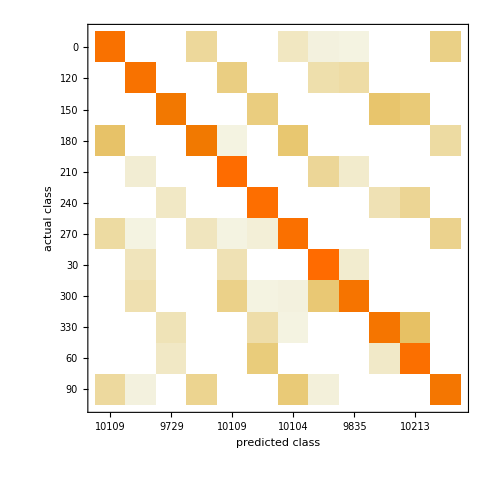

2. ImageNet dataset:
a. Choose 4000 images for training set. 400 for testing and 400 for validation. With rotation of 0, 90, 180, 270 deg.
The code for image processing is shown below. The same procedure is applied to test and validation sets as well.

```mathematica
listImages=Import["/Users/nguyen/Documents/all_tar_images/all_images/train/*.JPEG"];
cropTrainImage=ImageCrop[#,{224,224}]&/@listImages;
rotateAll[x_]:=Table[ImageRotate[x, i Degree, Background->None],{i,0,270,90}];
rotatedImage=rotateAll/@cropTrainImage;
labelList=Table[ ToString[i],Length[listImages],{i,0,270,90}];
imageWithLabel=Thread[Flatten[rotatedImage] -> Flatten[labelList]];
Length[imageWithLabel];
SetDirectory["/Users/nguyen/Documents"];
Export["trained_set10k_new.mx",imageWithLabel];
```

Use the Inception training model:

```mathematica
incept = NetTrain[inceptionNet, trainSet,All,BatchSize-> 100,Method-> "ADAM",ValidationSet->validateSet,MaxTrainingRounds->80,TargetDevice->"GPU"]
```

Result: accuracy 39%. Total training time 1.7 h. Rounds: 80 rounds. Batches: 12800. Method: ADAM.
The confusion matrix plot:

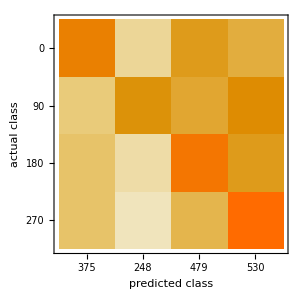

b, Choose 10000 images, but I did not carefully choose the image category. There are several categories, such as flowers, mushroom, etc. Adding these categories into the training make the result become worse and not much improvement compare with 4000 images.

So I remove hard-categories (as mentioned above). I use 10000 images for training, 1000 images for testing and 1000 images for validation from ImageNet data. Rotation from 0 to 270 in step of 90 deg.
An accuracy of 90% is achieved.
The confusion matrix is shown below

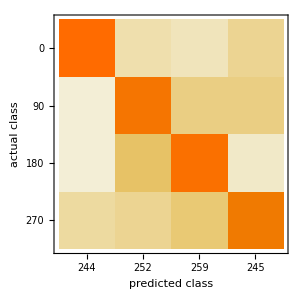

3. Google dataset. Dataset is downloaded from the website below. I only use part 1 and 2 from the sets.
["http://www.cs.ucf.edu/~aroshan/index_files/Dataset_PitOrlManh/zipped%20 images/"](http://www.cs.ucf.edu/~aroshan/index_files/Dataset_PitOrlManh/zipped%20 images/)

Choose 10k images for training. The code to do image processing is shown below. Same procedure is applied to test and validation sets.

```mathematica
imgRaw=Import["/Users/nguyen/Documents/google_street/train_set/*.jpg"];
imgResize=ImageResize[#,{300,300}]&/@imgRaw;
imgCrop=ImageCrop[#,{224,224}]&/@imgResize;
rotateAll[x_]:=Table[ImageRotate[x, i Degree, Background->None],{i,0,270,90}];
rotatedImage=rotateAll/@imgCrop;
labelList=Table[ ToString[i],Length[imgRaw],{i,0,270,90}];
imageWithLabel=Thread[Flatten[rotatedImage] -> Flatten[labelList]];
SetDirectory["/Users/nguyen/Documents"];
Export["train_set_goolgeImage.mx",imageWithLabel];
```

Training with Ademxapp. Due to limited memories in my computer, my mentor helped me with training, which is done in her computer.

```mathematica
ademt=Import["/Users/tuseetab/Downloads/adem10kgoogl.wlnet"]
testdata=Import["/Users/tuseetab/Downloads/test_set_googleImage.mx"];
testdata2=testdata[[;;1000]];
result=ClassifierMeasurements[ademt,testdata2];
result["Accuracy"]
result["ConfusionMatrixPlot"]
```

Many information on this project is followed the following link
["https://d4nst.github.io/2017/01/12/image-orientation/"](https://d4nst.github.io/2017/01/12/image-orientation/)

#### Code

Provide one of:

["https://github.com/nguyenton68/Summer2018Starter"](https://github.com/nguyenton68/Summer2018Starter)

#### Written Content / Lesson Plans

#### Conclusions in Detail

#### All Visualizations

#### Data Sources Links/References

#### Future Directions

#### Background Info Links/References

#### Keywords

Provide keywords as items

< keyword 1 >

< keyword 2 >

#### Other information